Atomic units

```mathematica
hbar=1.;
m = 1.;
e = 1.;
```

Coupling term

```mathematica
s1[n_,m_] := (Sin[(n+m)*Pi/2]/ (n+m)^2);
s2[n_,m_] := (Sin[(n-m)*Pi/2]/ (n-m)^2);
coup[n_,m_] := s1[n,m]- s2[n,m];
x[n_,m_,l_] := 2*l*coup[n,m]/Pi^2;
```

Energy levels

```mathematica
eN[n_,l_]:= Pi^2 * n^2 / (2*l^2);
```

10.3696

Transition frequency

```mathematica
wnm[n_,m_,l_] := eN[n,l] - eN[m,l];
```

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2. encountered.

Power::infy: Infinite expression 1/0.^2. encountered. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/infy",
ButtonNote->"Power::infy"]

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Indeterminate

Electric field coupling

```mathematica
alpha[q_,e0_,xnm_] := -q*e0*xnm;
```

Coeff differential equation system

```mathematica
q = -1;
e0 = 8;
l = 5;

omega0 = wnm[2,1,l];
omegaE = omega0*1;
alpha21 = alpha[1,e0,x[1,2,l]]

ode1 = D[c1[t],t] == -I*c2[t]*Exp[-I*omega0*t]*Cos[omegaE*t]*alpha21;
ode2 = D[c2[t],t] == -I*c1[t]*Exp[I*omega0*t]*Cos[omegaE*t]*alpha21;

N[omega0]
```

-640/(9 π^2)

0.592176

```mathematica
ics = {c1[0] == 1, c2[0] == 0};
tmax = 20;
sol = NDSolve[{ode1,ode2,ics},{c1[t],c2[t]},{t,0,tmax}]
```

{{c1[t]→InterpolatingFunction[{{0., 20.}}, <>][t],c2[t]→InterpolatingFunction[{{0., 20.}}, <>][t]}}

Cos[(3 π^2 t)/50]^2

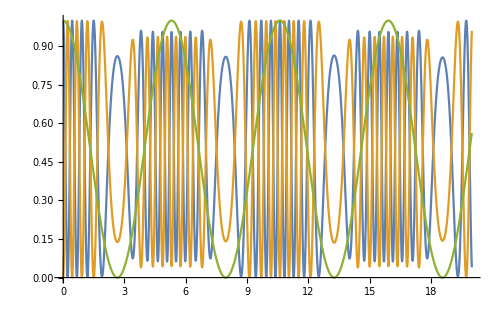

```mathematica
y1 = Abs[c1[t]]^2 /. Part[Part[sol,1],1];
y2 = Abs[c2[t]]^2 /. Part[Part[sol,1],2];
field[t_] = Cos[omegaE*t]^2 
Plot[{y1,y2,field[t]},{t,0,tmax}]
```

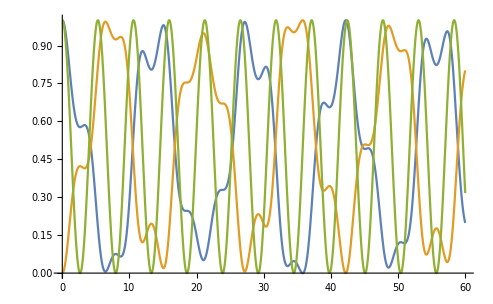

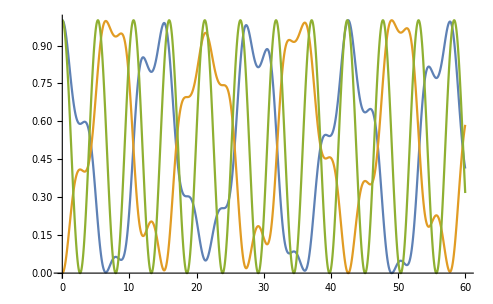

```mathematica
Plot[{y1p,y2p,field[t]},{t,0,tmax}]
Plot[{y1,y2,field[t]},{t,0,tmax}]
```

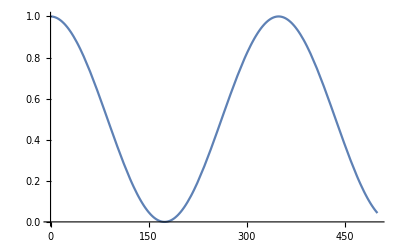

-Graphics-

-0.00321124+0.0266318 ⅈ